SquareWave[0.2 t]

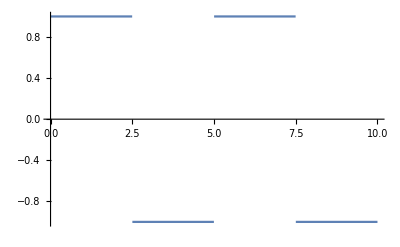

```mathematica
(*f = TriangleWave[0.3*t]*)
f = Sin[t]
(*f = SquareWave[0.2*t]*)
Plot[f,{t, 0,10}]
```

```mathematica
SquareWave[0.2*t]
```

SquareWave[0.2 t]

```mathematica
Manipulate[Table[ComplexListPlot[Table[f Exp[I ω t],{t,0,l,.01}],Joined->s, PlotRange->{{-1.1,1.1},{-1.1,1.1}}],{s,{False,True}}][[2]],{ω, 0.5, 2}, {l,0.5,50}]
```